# De Sitter Greens Functions (d=3)

## Setup:

```mathematica
SetDirectory["~/Documents/Causal/"];(*Directory should be set to where the causet2.wl package is saved*)
<<"causet2.wl";(*importing the package causet2.wl which has things like the sprinkling and causal/link matrices defined in it*)
```

```mathematica
m:=0
h:=1.3
n:=5000
d:=3
l:=1
"causal events" n
"~ causal relations" n^2
A=CSDeSitterDGlobalSlabFull[h,d,n];
ρ:=CSize[A] / CVolume[A]
"density" ρ
Subscript[C, 1]=SparseArray[CausalMatrix[A]];
```

5000 causal events

25000000 ~ causal relations

25.7378 density

```mathematica
V=(IdentityMatrix[n]+Subscript[C, 1]).(IdentityMatrix[n]+Subscript[C, 1]);
Tau[Vol_?NumericQ]:=Piecewise[{{τ/. FindRoot[Vol==2 Pi (τ/2-Tanh[τ/2]),{τ,1}],Vol>0},{0,Vol==0}}]
VolTimeFlat=N[(12/Pi)^(1/3)*(V)^(1/3)];
(*VolTime=Table[Piecewise[{{Tau[V[[i,j]]],V[[i,j]]>0},{0,V[[i,j]]==0}}],{i,n},{j,n}];

VolTime= Table[Tau[V[[i,j]]],{i,n},{j,n}];
VolTime=VolTime*Subscript[C, 1];
*)
(*Kvol=Table[Piecewise[{{Cos[VolTimeFlat[[i,j]]*m]/(2π VolTimeFlat[[i,j]]),V[[i,j]]>0},{0,V[[i,j]]==0}}],{i,n},{j,n}];*)
```

$Aborted

## Longest Chain Propagator

```mathematica
L=LinkMatrix[A];
maxlength=SparseArray[Subscript[C, 1]]["NonzeroValues"];
positions=SparseArray[Subscript[C, 1]//Flatten]["NonzeroPositions"]//Flatten;
zeroCompare=Table[0,{i,1,n},{j,1,n}];
counter=1;
chains=L;

Do[
counter++;

chains=chains.L;(*finding chains of length i+1 composed of links*)

If[chains==zeroCompare,Break[]];(*if chains = 0, we can stop the loop, since no longer chains will be found*)

length=Flatten[chains][[positions]];(*flattening the matrix to a 1d array and finding only the entries corresponding to the positions of nonzero causal matrix entries*)

comparePositions=SparseArray[length//Flatten]["NonzeroPositions"]//Flatten;(*finding the positions in the new array that are nonzero*)

length=SparseArray[length]["NonzeroValues"];(*keeping only the nonzero entries of the new array*)

length=counter*HeavisideTheta[length];(*currently the length array has the number of link chains between two points, but we want the length of the chain*)
(*since the chains are longer in each iteration of the loop, we can replace the corresponding entries in the max length array with the updated values *)
maxlength[[comparePositions]]=length
(*looping up to NN-1 (i.e. L^(NN-1)), since the longest possible chain in a causet of size NN has NN-1 links*)
,{i,1,n-2}]

flattenedMaxLength=Table[0,{i,1,n*n}];(*NN^2 array of zeros*)

Do[flattenedMaxLength[[ positions[[i]] ]]=maxlength[[i]],{i,1,Length[positions]}];(*replace entries with max chain lengths according to the position of nonzero causal matrix entries in flattened causal matrix*)

MaxLength=Table[flattenedMaxLength[[1+(i-1)*n;;n+(i-1)*n]],{i,1,n}];(*unflatten to a square NN x NN matrix*)
m3=1.8701503305151406;
a=((ρ π)/12)^(1/3)m3/(2π);
K = Table[If[Subscript[C, 1][[i,j]]==1,(a*Cos[m/(2 π a)*MaxLength[[i,j]]])/MaxLength[[i,j]],0],{i,n},{j,n}];
(*K=K0.Inverse[IdentityMatrix[n]+m^2/ρ K0];*)
```

## Manifold Proper Time

```mathematica
MfdTime =Table[Re[ArcCosh[1/(Cos[A[[1,i,4]]]*Cos[A[[1,j,4]]])*(A[[1,i,1]]*A[[1,j,1]]+A[[1,i,2]]*A[[1,j,2]]+A[[1,i,3]]*A[[1,j,3]]-Sin[A[[1,i,4]]]*Sin[A[[1,j,4]]])]*Subscript[C, 1][[i,j]]],{i,n},{j,n}];

(*MfdSpace=Table[Im[ArcCosh[1/(Cos[A[[1,i,4]]]*Cos[A[[1,j,4]]])*(A[[1,i,1]]*A[[1,j,1]]+A[[1,i,2]]*A[[1,j,2]]+A[[1,i,3]]*A[[1,j,3]]-Sin[A[[1,i,4]]]*Sin[A[[1,j,4]]])]],{i,n},{j,n}];
MfdSpace= MfdSpace*(UpperTriangularize[ConstantArray[1,{n,n}],1]-Subscript[C, 1]);*)

(*time=Transpose[{Flatten[MfdSpace],Flatten[N[K]]}];*)

(*time=Transpose[{Flatten[MfdTime],Flatten[K]}];
time=DeleteCases[Chop[time],{0,_}];*)

(*timeVol=Transpose[{Flatten[MfdTime],Flatten[K0]}];
timevol=DeleteCases[Chop[timeVol],{0,_}];*)

Length[time]"No. of non-zero relations"
```

0

## Whitman function for Causet :

```mathematica
iΔ=N[I*(K-Transpose[K])];
{EE,VV}=Chop[Eigensystem[iΔ]];
Q = Transpose[VV] . DiagonalMatrix[Clip[N[EE],{0, Max[N[Abs[EE]]]}]] . Conjugate[VV] // Chop;

pointsTime=Transpose[{Flatten[MfdTime],Flatten[Re[Q]]}];
pointsTime=DeleteCases[Chop[pointsTime],{0,_}];
Length[pointsTime]"No. of non-zero relations"
(*pointsSpace=Transpose[{Flatten[MfdSpace],Flatten[Re[Q]]}];
*)
```

4880173 No. of non-zero relations

## Whitman function (Analytical):

```mathematica
Subscript[m, c]:=Sqrt[3]/2
M:= Sqrt[m^2+Subscript[m, c]^2]
d:=3
H1=(d-1)/2+Sqrt[((d-1)/2)^2-M^2 l^2];
H2=(d-1)/2-Sqrt[((d-1)/2)^2-M^2 l^2];
norm=Gamma[H1]*Gamma[H2]/((4*π)^(d/2)*l^2*Gamma[d/2]);
W[τ_]:=norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[τ])]
Wpodal[τ_]:=norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1-Cosh[τ])]
Walpha[τ_,α_,β_]:= Cosh[2α]*W[τ]+Sinh[2α]*(Cos[β]*Re[Wpodal[τ]]-Sin[β]*Im[Wpodal[τ]])
(*
Walpha[1,0,1]
Plot[Re[Walpha[τ,1,0]],{τ,0,8},PlotStyle->Orange]


Plot[Walpha[τ,1,1],{τ,0,8},PlotStyle->Orange]
1/2 ArcTanh[Abs[Sin[π*Sqrt[((d-1)/2)^2-M^2 l^2]]]]
(d/2+HeavisideTheta[-Sin[π*Sqrt[((d-1)/2)^2-M^2 l^2]]])π

N[Re[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[1])]]]
N[Limit[Re[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[ϵ])]],{ϵ->0}]]
*)
```

## Hadamard function (Re[W]):

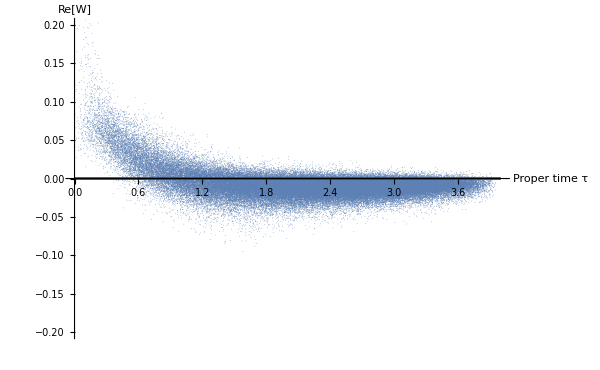

```mathematica
sample:=100000
plotLength := 4
PlottingPoints=RandomSample[pointsTime,sample];
Show[ListPlot[PlottingPoints,PlotStyle->PointSize[0.00001],ImageSize->600],Plot[Re[W[τ]],{τ,0,plotLength},PlotStyle->Red,PlotRange->{{0,plotLength},{-.2,.2}}],AxesOrigin->{0,0},PlotRange->{{0,plotLength},{-.2,.2}},AxesLabel->{"Proper time τ","Re[W]"}]
(*,Plot[Re[Walpha[τ,alpha,beta]],{τ,0,8},PlotStyle->Orange,PlotRange->{{0,8},{-.1,.1}}]*)
```

## Retarded Greens Functions:

RandomSample::lrwl: The set of items to sample from, time, should be a non-empty list or a rule weights -> choices.

General::stop: Further output of RandomSample::lrwl will be suppressed during this calculation.

ListPlot::lpn: RandomSample[time,100000.] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[RandomSample[time,100000],PlotStyle→PointSize[0.00001],PlotRange→{{0,4},{-1,1}}],,PlotRange→{{0,4},{-1,1}}].

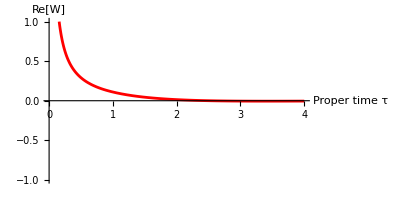
Show[ListPlot[RandomSample[time,100000],PlotStyle→PointSize[0.00001],PlotRange→{{0,4},{-1,1}}],-Graphics-,PlotRange→{{0,4},{-1,1}}]

```mathematica
sample:=100000
plotLength := 4
Show[ListPlot[RandomSample[time,sample],PlotStyle->PointSize[0.00001],PlotRange->{{0,plotLength},{-1,1}}],Plot[-2*Im[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[τ])]],{τ,0,plotLength},PlotStyle->Red,AspectRatio->Automatic,AxesLabel->{"Proper time τ","Re[W]"},PlotRange->{{0,plotLength},{-1,1}}],PlotRange->{{0,plotLength},{-1,1}}]
(*ListPlot[RandomSample[timeVol,sample],PlotStyle->{PointSize[0.00001],Orange},PlotRange->{{0,plotLength},{-1,1}}]*)
```

## Measuring m_3

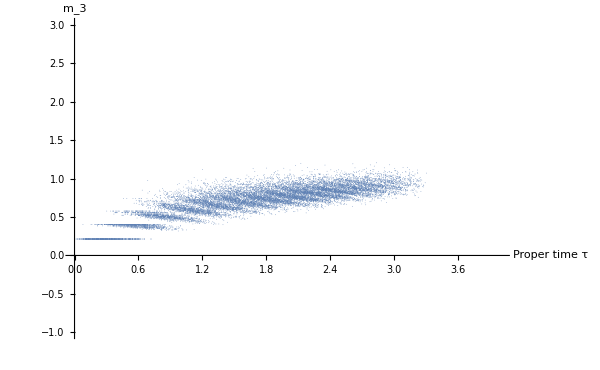

```mathematica
Ratio = Table[Piecewise[{{MaxLength[[i,j]]/(ρ*Tau[V[[i,j]]])^(1/d),V[[i,j]]>0},{0,V[[i,j]]==0}}],{i,n},{j,n}];
RatioTime=Transpose[{Flatten[MfdTime],Flatten[N[Ratio]]}];
sample:=100000
plotLength := 4
PlottingPoints=RandomSample[RatioTime,sample];
Show[ListPlot[PlottingPoints,PlotStyle->PointSize[0.00001],ImageSize->600],PlotRange->{{0,plotLength},{-1,3}},AxesLabel->{"Proper time τ","m_3"}]
```